```mathematica
DSolve[y'[x]==-3y[x]+x+E^(-2x),y[x],x]
```

```mathematica
f={{y[x]->ⅇ^(-3 x) (ⅇ^x+ⅇ^(3 x) (-1/9+x/3))+ⅇ^(-3 x) C[1]}}
```

{{y[x]→ⅇ^(-3 x) (ⅇ^x+ⅇ^(3 x) (-1/9+x/3))+ⅇ^(-3 x) C[1]}}

```mathematica
g[x_]:=f[[1,1,2]]
```

```mathematica
Expand[g[x]]
```

-1/9+ⅇ^(-2 x)+x/3+ⅇ^(-3 x) C[1]

```mathematica
Solve[y==%,C[1]]
```

{{C[1]→-1/9 ⅇ^x (9-ⅇ^(2 x)+3 ⅇ^(2 x) x-9 ⅇ^(2 x) y)}}

```mathematica
Expand[%]
```

{{C[1]→-ⅇ^x+ⅇ^(3 x)/9-1/3 ⅇ^(3 x) x+ⅇ^(3 x) y}}

```mathematica
constante[x_,y_]=-ⅇ^x+ⅇ^(3 x)/9-1/3 ⅇ^(3 x) x+ⅇ^(3 x) y;
```

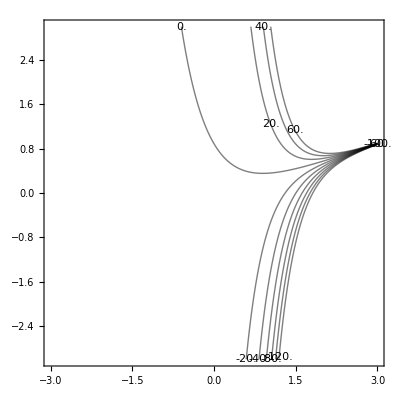

```mathematica
ContourPlot[constante[x,y],{x,-3,3},{y,-3,3},Contours->10,ContourShading->False,ContourLabels->True,PlotPoints->100]
```

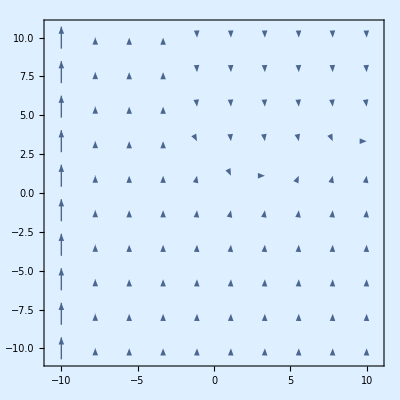

```mathematica
VectorPlot[{1,-3y+x+E^(-2x)},{x,-10,10},{y,-10,10},StreamStyle->{Arrowheads[.02],Thin,Blue,Tiny},Background->LightBlue,VectorScale->{.05,.1},VectorPoints->10]
```

```mathematica
stream=StreamPlot[{1,-3y+x+E^(-2x)},{x,-1/2,1/2},{y,-1/2,1/2},StreamStyle->{Arrowheads[.02],Thin,Blue,Tiny},Background->LightBlue];
```

```mathematica
contorno=ContourPlot[{constante[x,y]==8,constante[x,y]==-8/9},{x,-10,10},{y,-10,10},ContourStyle->{{Thick,Red},{Thick,Red}},PlotPoints->50];
```

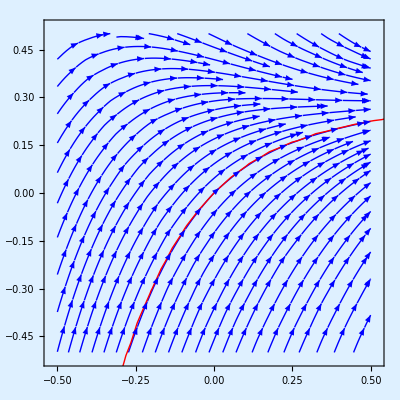

```mathematica
Show[stream,contorno]
```